/home/kempsilonnaught/Builds/CellSurfaceFE/MongeParameterization/SimpleTwoInclusionLift

{{100,4.00877×10^6},{115,4.00922×10^6},{130,4.00934×10^6},{145,4.00963×10^6},{160,4.00983×10^6},{175,4.0101×10^6},{190,4.01027×10^6},{205,4.0105×10^6},{220,4.01072×10^6},{235,4.01095×10^6},{250,4.0111×10^6},{265,4.01126×10^6},{280,4.01135×10^6},{295,4.01149×10^6},{310,4.01166×10^6},{325,4.01164×10^6},{340,4.01206×10^6},{355,4.01201×10^6},{370,4.01209×10^6},{385,4.01248×10^6},{400,4.01262×10^6},{415,4.01249×10^6},{430,4.01253×10^6},{445,4.01283×10^6},{460,4.01276×10^6},{475,4.01279×10^6},{490,4.01289×10^6},{505,4.01299×10^6},{520,4.01311×10^6},{535,4.0132×10^6},{550,4.01328×10^6},{565,4.01337×10^6},{580,4.01371×10^6},{595,4.01379×10^6},{610,4.01386×10^6},{625,4.01393×10^6},{640,4.01399×10^6},{655,4.01404×10^6},{670,4.01411×10^6},{685,4.01411×10^6},{700,4.01419×10^6},{715,4.01426×10^6},{730,4.01429×10^6},{745,4.01433×10^6},{760,4.0143×10^6},{775,4.01433×10^6},{790,4.01441×10^6},{805,4.01444×10^6},{820,4.01446×10^6},{835,4.01441×10^6},{850,4.01442×10^6},{865,4.01443×10^6},{880,4.01447×10^6},{895,4.01443×10^6},{910,4.01448×10^6},{925,4.0145×10^6},{940,4.01448×10^6},{955,4.01451×10^6},{970,4.0146×10^6},{985,4.0146×10^6},{1000,4.0146×10^6}}

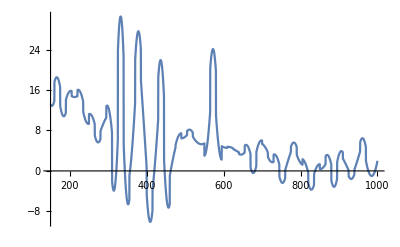

```mathematica
SetDirectory[NotebookDirectory[]]
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]]];
{plot1,plot2}
]
files=Drop[Drop[FileNames[],1],-27];
allPlots=Table[ViewSurface[file],{file,files}];
ListAnimate[allPlots]
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
]
Print[SolveForce["energysep.txt"]]
energysepfunc = Interpolation[SolveForce["energysep.txt"]];
forcefunction = energysepfunc';
Plot[forcefunction[x], {x, 150, 1000}]
```